## 3D Spheroid Simulator

```mathematica
ClearAll["Global`*"];
```

```mathematica
$Version
```

12.1.0 for Microsoft Windows (64-bit) (March 14, 2020)

## Misc F(x)

```mathematica
initCubicGrid[npart_]:=Block[{L=15,pos},
pos=L RandomVariate[NormalDistribution[],{npart,3}];
{L,pos}
];
```

```mathematica
randGaussRad[μ_,σ_]:=Block[{randrad},
randrad=RandomVariate[NormalDistribution[]];
randrad = μ + (randrad σ);
randrad
];
```

## Force Function

```mathematica
ForceParams[coords_,rad_,poisson_,modulus_,receptor_,ligand_,nPart_]:= Block[{etab,spDistMat,f,cellindsAround,neighbourpos,dist,
sliceMat,cellpos,RijHat,hij,radc,Eij,modc,poissc,Rijf,rado,areaint,invDr2,forceFact,ligandc,receptorc,pressureFact,pressure,
force,res,gamma,mag,posSel,distE,neighbourposE,cellindsAroundE,fposSel},

force=gamma=pressure=ConstantArray[0,Length@coords];
etab = 0.0001;
f = 0.0001; (* adhesion parameter f^{ad} *)
spDistMat=SparseArray[DistanceMatrix@coords]; (* distance between all cells *)

Do[
cellpos=coords[[part]];
radc=rad[[part]];
poissc=poisson[[part]];
modc=modulus[[part]];
ligandc=ligand[[part]];
receptorc=receptor[[part]];

sliceMat=spDistMat[[part]];
cellindsAround=Range[Length@coords];
neighbourpos=coords[[cellindsAround]];
dist=Normal@sliceMat;
posSel=Position[MapThread[#1+radc-#2&,{rad,dist}],x_/;x>0.0];
fposSel=Flatten@posSel;
If[Length[fposSel]>0,
distE=Extract[dist,posSel];
neighbourposE=Extract[neighbourpos,posSel];
cellindsAroundE=Extract[cellindsAround,posSel];
Do[
If[distE[[i]]≠ 0,
RijHat= (cellpos-neighbourposE[[i]])/distE[[i]];
rado=rad[[ Part[cellindsAroundE,i] ]];
hij=(rado+radc-distE[[i]]);
Eij=((1-poisson[[ Part[cellindsAroundE,i] ]]^2)/(modulus[[ Part[cellindsAroundE,i] ]]) + (1-poissc^2)/(modc));
Rijf=(1/radc + 1/rado);
areaint=π (1/Rijf)hij;
invDr2=hij^(1.5);
forceFact=(invDr2/(0.75(Eij)Sqrt[Rijf]))-areaint*f*0.5(receptor[[ Part[cellindsAroundE,i] ]] ligandc + receptorc ligand[[ Part[cellindsAroundE,i] ]]);
pressureFact=Abs[forceFact/areaint];
force[[part]]+= (forceFact*RijHat);
pressure[[part]]+=pressureFact
],{i,Length@posSel}
];
];

mag=Norm[force[[part]]];

If[Length[fposSel]>0,
Do[
If[distE[[i]]≠0,
RijHat= (cellpos-neighbourposE[[i]])/distE[[i]];
rado=rad[[ Part[cellindsAroundE,i] ]];
hij=(rado+radc-distE[[i]]);
Rijf=(1/radc + 1/rado);
areaint=π (1/Rijf)hij;

gamma[[part]]+=etab*areaint*0.5*(1+Total[(force[[part]]*RijHat)]/mag)*0.5*(receptor[[ Part[cellindsAroundE,i] ]]*ligandc + receptorc*ligand[[ Part[cellindsAroundE,i] ]])
],{i,Length@posSel}
];
];
,{part,nPart}];
{force,pressure,gamma}
];
```

## Visualization

```mathematica
Clear@plotRadii;
plotRadii[{keys_,rad_,pos_}]:=Block[{r},
r=Rescale@rad;
Graphics3D[
MapThread[{Opacity[RandomReal[{0.75,1.0}]],ColorData["Rainbow"][#3],Ball[#2,#1]}&,{rad,pos,r}],
ImageSize->Medium
]
];
```

```mathematica
Clear@plotPressure;
plotPressure[{rad_,pos_,pressure_}]:=Block[{p},
p=Rescale@pressure;
Graphics3D[
MapThread[{Opacity[RandomReal[{0.5,1.0}]],ColorData["Rainbow"][#3],Ball[#2,#1]}&,{rad,pos,p}],
ImageSize->Medium
]
];
```

```mathematica
getParticleTraj[trackVec_,key_]:= Block[{ind,rad,pos,pressure,temp},
Map[
({ind,rad,pos,pressure}=trackVec[#1];
temp=AssociationThread[ind,pos];
Lookup[temp,key,Nothing])&,Range@Length[trackVec]
]
]
```

```mathematica
getParticleRad[trackVec_,key_]:= Block[{ind,rad,pos,pressure,temp},
Map[
({ind,rad,pos,pressure}=trackVec[#1];
temp=AssociationThread[ind,rad];
Lookup[temp,key,Nothing])&,Range@Length[trackVec]
]
]
```

```mathematica
Clear@getParticlePressure;
getParticlePressure[trackVec_,key_]:= Block[{ind,rad,pos,pressure,temp},
Map[
({ind,pressure}={trackVec[#][[1]],trackVec[#+1][[-1]]};
temp=AssociationThread[ind,pressure];
Lookup[temp,key,Nothing])&,
Range[Length[trackVec]-1]
]
]
```

## Main

```mathematica
trackVector=<||>;
nSteps=1000;
Block[{numin,nPart,density,mass,nDim,dt,dt2,sampleFreq,sampleCounter,printFreq,radmitosis,η,gfac,taumin,L,pos,vel,rad,modulus,poisson,receptor,ligand,lifetime,time,volrate,keys,trackAssoc,deadlist,cellseverinvolved,centerM,force,pressure,gamma,gammat,temp,death,deadpart,deadnumin,grate,a,b,r2,r3,r4,r5,pt,vels},
numin=200;
(* set configuration parameters *)
nPart=numin; (* number of particles *)
density = 0.001; (* density of particles *)
mass = 1; (* particle mass *)
nDim = 3; (* dimensionality of the system (3D) *)

(* set simulation parameters *)
dt = 10.0; (* integration time *)
dt2 = dt^2; (* square of integration period *)
(* nSteps = 3800; (* total simulation time in integration steps*) *)
sampleFreq= 100; (* sampling frequency *)
sampleCounter = 1; (* sampling counter *)
printFreq = 100; (* printing frequency *)
(* volrate = 1.4 (* rate of volume growth dv/dt *) *)
radmitosis = 5.0; (* mitotic radius or critical size *)
η = 0.005; (* ECM viscosity *)
gfac= 1.0;
taumin = gfac*54000; (* second - minimum cell cycle time *)
 {L,pos}=initCubicGrid[nPart];
vel=ConstantArray[0,{nPart,nDim}];
(* radomly assign a radius to each particle *)
{rad,modulus,poisson,receptor,ligand,lifetime}=Transpose@ParallelTable[
{randGaussRad[4.5,0.5],randGaussRad[0.001,0.0001],randGaussRad[0.5,0.02],randGaussRad[0.9,0.02],randGaussRad[0.9,0.02],0},{i,nPart}];

(* Molecular Dynamics *)
time = 0; (* following simulation time *)
volrate= (2 π radmitosis^3)/(3 taumin);
keys=Range[nPart];
trackAssoc=AssociationThread[keys->pos];
deadlist=CreateDataStructure["DynamicArray"];
cellseverinvolved=nPart;

Do[
nPart=Length@pos;
centerM = {0,0,0};
(* calculate new forces *)
{force,pressure,gamma}=ForceParams[pos,rad,poisson,modulus,receptor,ligand,nPart];
gammat = 0;
(* Implement Anderson Thermostat *)
Do[
gammat=6 π η rad[[part]] + gamma[[part]];
(* dropping the inertial term and updating the coords *)
temp=force[[part]];
pos[[part]]+= (dt*temp)/gammat;
(* updating velocities *)
vel[[part]]=temp/gammat;
lifetime[[part]]+=dt,
{part,nPart}
];
(* Update the size of the particles - all radii updated at one time *) 
death = 10^-6;
deadpart=0;
deadnumin=0;
Do[
Which[RandomReal[]≤ death*dt,
(* Death *)
deadpart+=1;
deadlist["Append",part],
(* Growth *)
(rad[[part]]<radmitosis)&&(pressure[[part]]<0.0001),
grate= volrate/(4.0 π rad[[part]]^2);
rad[[part]]+= dt*randGaussRad[grate,10^-5],
(* Division *)
(rad[[part]]≥radmitosis)&&(pressure[[part]] <0.0001),
AppendTo[rad,(2^(-1./3))*rad[[part]]];
rad[[part]]*=(2^(-1./3));
AppendTo[modulus,randGaussRad[0.001,0.0001]];
AppendTo[poisson,randGaussRad[0.5,0.02]];
AppendTo[receptor,randGaussRad[0.9,0.02]];
 AppendTo[ligand,randGaussRad[0.9,0.02]];
AppendTo[lifetime,0];
cellseverinvolved+=1;
AppendTo[keys,cellseverinvolved];
AppendTo[vel,{0.,0.,0.}];
a=0;b=1;
r3=(b-a)RandomReal[] + a;
r4= π(b-a)RandomReal[] + π a;
r5=2 π(b-a)RandomReal[]+2 π a;
pt= {pos[[part,1]]+radmitosis*(1-2^(-1./3))Sin[r4]Cos[r5],
pos[[part,2]]+radmitosis*(1-2^(-1./3))Sin[r4]Sin[r5],
pos[[part,3]]+radmitosis*(1-2^(-1./3))Cos[r4]};
AppendTo[pos,pt];
pt={pos[[part,1]]-radmitosis*(1-2^(-1./3))Sin[r4]Cos[r5],
pos[[part,2]]-radmitosis*(1-2^(-1./3))Sin[r4]Sin[r5],
pos[[part,3]]-radmitosis*(1-2^(-1./3))Cos[r4]};
pos[[part]]=pt],
{part,nPart}
];

If[deadpart>0,
{pos,rad,modulus,poisson,receptor,ligand,vels,keys}=ReplacePart[#,Thread[Normal[deadlist]-> Nothing]]&/@{pos,rad,modulus,poisson,receptor,ligand,vels,keys};
];
trackVector[step]={keys,rad,pos,pressure};
time += dt,{step,nSteps}]
];//AbsoluteTiming
```

{139.563,Null}

```mathematica
plotPressure@Rest@trackVector[nSteps]
```

-Graphics3D-

```mathematica
Max@*First@trackVector[nSteps]
```

239

```mathematica
arrows={Arrow@getParticleTraj[trackVector,#]}&/@Range[Max@*First@trackVector[nSteps]];
```

```mathematica
Graphics3D[{Arrowheads[Small],Thin,arrows},ImageSize->Medium]
```

-Graphics3D-

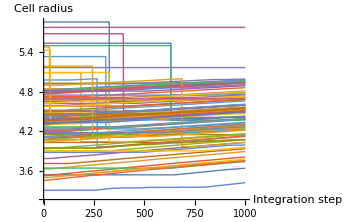

```mathematica
getParticleRad[trackVector,#]&/@Range[100]//ListLinePlot[#,PlotStyle->Thin,ImageSize->Medium,
AxesLabel->{"Integration step","Cell radius"}]&
```

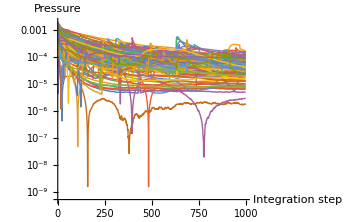

```mathematica
getParticlePressure[trackVector,#]&/@Range[100]//ListLogPlot[#,Joined->True,PlotStyle->Thin,
PlotRange->All,ImageSize->Medium,AxesLabel->{"Integration step","Pressure"}]&
```